## Wehrens - Krah: The (co)variance Checker

#### Introduction

This notebook checks the variances and cross-correlations as obtained analytically with an answer that is completely conjured by Mathematica itself. Mathematica’s version is, of course, correct, but not very insightful. The analytical solution is error-prone, yet much more insightful.

The model is written down in Fourier Space, and each Ni denotes the fourier transform of an independent Ornstein-Uhlenbeck noise source.

This model is an extension from the model in Kiviet et al, but a simplification of the model by Wehrens (PhD thesis). It involves three proteins: the C-sector and it’s reporter (y) and a constitutive reporter (h). Only the C-reporter is metabolically active, but it shares a noise source with its reporter (Ns, which models CRP noise), so traces of the metabolic activity of the C-sector can be seen when analysing its reporter y. Moreover, this notebook contains all researched extensions analytically. Here, α1 represents single-cell resource competition, and α2,  can be used to also make global noise cause competition. Note that a  realistic model might have TMπH = TMπ and α2 = 0. We write L = α1 (Ns + (TR + α2 TMπ) δM/M0)) in this document. In the main text and in the supplementary file, L = 0.

δλ/λ0 = TMλ δM/M0+Nλ
δM/(,M0) = TCM δϕC/ϕC0 + NM
δπc/πc0 = (TMπ+ TR) δM/M0 + Nπc + Ns
δπy/πy = (TMπ+ TR)δM/M0+Nπy + Ns 
δπh/πh0 = TMπH δM/M0+Nπh - α1 (Ns + (TR+α2 TMπ)δM/M0)
δϕi/ϕi0= λ0/(λ0+ⅈ ω)(δπi/πi0- δλ/λ0)

```mathematica
SetOptions[Plot,{PlotRange->All,PlotStyle-> {{AbsoluteThickness[5]},{AbsoluteThickness[2],Dashed}},Frame-> True,FrameStyle-> Thick,FrameTicks-> None,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 300,AspectRatio-> .9}];
SetDirectory[NotebookDirectory[]];
```

## Mathematica’s solution

#### Defining the system, parameters and noise sources

```mathematica
Clear["Global`*"]
$Assumptions = {λ0 >0,TCM (TR+TMπ-TMλ)<1, βπc>0,βs>0, βπy>0, βπh>0,  βM>0,βλ>0,TMπ ∈ Reals,TMπH ∈ Reals,TCM∈ Reals,TMλ∈ Reals,TR∈ Reals, α1≥0, α2≥0 ,θπc≥ 0, θs≥ 0,θπy≥ 0,θπh≥ 0,θM≥ 0,θλ≥ 0,TMλ ≠ TR + TMπ};
```

```mathematica
Tϕλ = -1;
δsol=FullSimplify[Solve[{ 
δλ == TMλ δM +Nλ,
δM == TCM δϕc + NM, 
δπc ==  Nπc +Ns+ (TMπ +TR)δM ,
 δπy ==  Nπy +Ns+ (TMπ +TR)δM, 
δπh == Nπh+(TMπh -α1(TR+ α2 TMπ))δM - α1 Ns,
 δϕc== λ0/(λ0+ⅈ ω)(δπc+Tϕλ δλ),
δϕy== λ0/(λ0+ⅈ ω)(δπy+Tϕλ δλ),
δϕh== λ0/(λ0+ⅈ ω)(δπh+Tϕλ δλ)},{δλ,δM,δϕc, δϕy,δϕh,δπc,δπy,δπh}]][[1]];
```

$Aborted

```mathematica
Sδsol = FullSimplify[δsol];

Nrep = {Nπc^2 -> θπc^2/(βπc^2+ω^2),Ns^2-> θs^2/(βs^2+ω^2),Nπy^2 -> θπy^2/(βπy^2+ω^2),Nπh^2 -> θπh^2/(βπh^2+ω^2),NM^2-> θM^2/(βM^2+ω^2),Nλ^2-> θλ^2/(βλ^2+ω^2)};
Nsources = {Nπc,Ns,Nπy,Nπh,NM,Nλ};
Npar= {θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ};
Tpar= {TR,TMπ,TMπh,TCM,TMλ,α1,α2};
```

#### Creating the functions

First, we define a function that prepares the parameters in such a way that the fourier transforms can be taken:

```mathematica
parrep[parN_,parT_]:=Join[Table[Npar[[i]]-> parN[[i]],{i,1,Length[Npar]}],Table[Tpar[[i]] -> parT[[i]],{i,1,Length[Tpar]}]]
```

We now define two functions that together create the cross-correlations:

```mathematica
prepIFT[v1_,v2_]:=(Total[FullSimplify[Coefficient[ComplexExpand[v1* v2 /.Sδsol],#,2] #^2&/@ Nsources]]//.Nrep)
DoF[v1_,v2_]:={Assuming[t>0,InverseFourierTransform[prepIFT[v1,v2],ω,t, FourierParameters-> {1,-1}]],Assuming[t<0,InverseFourierTransform[prepIFT[v1,v2],ω,t, FourierParameters-> {1,-1}]]}/.{t-> τ}
DoFVar[v1_,v2_]:=1/(2 π)Integrate[prepIFT[v1,v2],{ω,-∞,∞}]
```

#### Coefficients of Variation

CRP-sector

```mathematica
ϕcϕct = DoFVar[δϕc,δϕc];
Xϕcϕc[parN_,parT_,λ0f_]:=ϕcϕct /.parrep[parN,parT]/.{λ0-> λ0f}
πcπct = DoFVar[δπc,δπc];
Xπcπc[parN_,parT_,λ0f_]:=πcπct/. parrep[parN,parT]/.{λ0-> λ0f}
λλt = DoFVar[δλ,δλ];
Xλλ[parN_,parT_,λ0f_]:=λλt/. parrep[parN,parT]/.{λ0-> λ0f}
```

Y-reporter

```mathematica
ϕyϕyt = DoFVar[δϕy,δϕy];
Xϕyϕy[parN_,parT_,λ0f_]:=ϕyϕyt /.parrep[parN,parT]/.{λ0-> λ0f}
πyπyt = DoFVar[δπy,δπy];
Xπyπy[parN_,parT_,λ0f_]:=πyπyt/. parrep[parN,parT]/.{λ0-> λ0f}
```

H-reporter

```mathematica
ϕhϕht = DoFVar[δϕh,δϕh];
Xϕhϕh[parN_,parT_,λ0f_]:=ϕhϕht /.parrep[parN,parT]/.{λ0-> λ0f}
πhπht = DoFVar[δπh,δπh];
Xπhπh[parN_,parT_,λ0f_]:=πhπht/. parrep[parN,parT]/.{λ0-> λ0f}
```

#### Cross-covariances

CRP-sector and Growth (λ)

```mathematica
ϕcλt=DoF[δϕc,δλ];
Xϕcλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{ϕcλt[[1]]/.{τ-> t},t≥ 0},{ϕcλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}

πcλt=DoF[δπc,δλ];
Xπcλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{πcλt[[1]]/.{τ-> t},t≥ 0},{πcλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}
```

CRP-reporter (Y) and Growth (λ)

```mathematica
ϕyλt=DoF[δϕy,δλ];
Xϕyλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{ϕyλt[[1]]/.{τ-> t},t≥ 0},{ϕyλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}

πyλt=DoF[δπy,δλ];
Xπyλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{πyλt[[1]]/.{τ-> t},t≥ 0},{πyλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}
```

Constitutive-reporter (H) and Growth (λ)

```mathematica
ϕhλt=DoF[δϕh,δλ];
Xϕhλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{ϕhλt[[1]]/.{τ-> t},t≥ 0},{ϕhλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}

πhλt=DoF[δπh,δλ];
Xπhλ[t_,parN_,parT_,λ0f_]:=Piecewise[{{πhλt[[1]]/.{τ-> t},t≥ 0},{πhλt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}
```

Y and H reporters

```mathematica
ϕhϕyt = DoF[δϕh,δϕy];
Xϕhϕy[t_,parN_,parT_,λ0f_]:=Piecewise[{{ϕhϕyt[[1]]/.{τ-> t},t≥ 0},{ϕhϕyt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}

πhπyt = DoF[δπh,δπy];
Xπhπy[t_,parN_,parT_,λ0f_]:=Piecewise[{{πhπyt[[1]]/.{τ-> t},t≥ 0},{πhπyt[[2]]/.{τ-> t},t<0}}]/. parrep[parN,parT]/.{λ0-> λ0f}
```

## Analytical functions

The functions below are as analytically calculated in the Supplementary information for Wehrens and Krah et al; “Dynamical regulation in bacterial cells during steady state growth”.
Here, we have additionally included  L , which is 0 zero in the main text and supplement.

#### Analytical Coefficients of variation

CRP-sector

```mathematica
η2ϕC=λ0^2/(2 λE)(θπc^2/(βπc (βπc+λE))+ θs^2/(βs(βs+λE))+TMC^2 θM^2/(βM(βM+λE))+θλ^2/(βλ(βλ+λE)));

η2πC=θπc^2/(2 βπc)(1+ (2 λ0)/(βπc + λE) TCM (TR + TMπ)) + θs^2/(2 βs)(1+ (2λ0)/(βs + λE) TCM (TR+ TMπ)) + θM^2/(2 βM)(TR + TMπ)^2(1+ (2 λ0)/(βM + λE)TCM TMC) + TCM^2(TR + TMπ)^2 η2ϕC;

η2λ=θλ^2/(2 βλ)(1-(2 λ0)/(βλ+λE)TCM TMλ) +θM^2/(2 βM)TMλ^2(1+ (2λ0)/(βM+λE)TCM TMC) +TCM^2 TMλ^2 η2ϕC;
```

Y-reporter

```mathematica
η2ϕy=θπy^2/(2 βπy)λ0/(βπy + λ0) + θπc^2/(2βπc)λ0/(βπc+λ0)λ0^2 TCM^2 TMC^2 (βπc+λ0 + λE)/((βπc+λE)λE(λ0+λE))+ θs^2/(2 βs) λ0/(βs+λ0)(1+ TCM TMC (λ0(βs + λ0 + λE))/(λE( βs + λE))) + θM^2/(2 βM) λ0/(βM + λ0)TMC^2(1+ TCM TMC (λ0(βM+λ0+λE))/(λE(βM+λE))) + θλ^2/(2βλ)λ0/(βλ+λ0)(1+ TCM TMC (λ0(βλ + λ0+λE))/(λE(βλ+λE))) ;

η2πy=θπy^2/(2 βπy) + θs^2/(2 βs)(1+2 λ0/(βs+λE)TCM (TR + TMπ)) + θM^2/(2 βM)(TR + TMπ)^2(1+2 λ0/(βM+λE) TCM TMC) + TCM^2(TR+ TMπ)^2 η2ϕC;
```

H-reporter

```mathematica
η2ϕh =(θπh^2 λ0)/(2 βπh (βπh+λ0))  +(α1 θs^2 λ0)/(2 βs (βs+λ0))(α1 -TCM(TMπh-L-TMλ)(2λ0(βs+λ0+λE))/((βs+λE) (λ0+λE)))+(λ0^3 TCM^2(TMπh - L-TMλ)^2)/(2 λE(λ0+λE))((θπc^2(βπc + λ0 + λE))/(βπc(βπc+λ0)(βπc+λE)) +(θs^2(βs+λ0+λE))/(βs(βs+λ0)(βs+λE)))+
(θM^2 λ0(TMπh-L- TMλ)^2)/(2 βM(βM+λ0))(1+ TCM TMC (λ0(βM+λ0+λE))/(λE(βM+λE))) + (θλ^2 λ0)/(2 βλ(βλ+λ0))(1+ TCM (TMπh-L-TMλ)(λ0(βλ+λ0+λE))/((βλ+λE)(λ0+λE))(TCM(TMπh-L-TMλ)λ0/λE+2));


η2πh =θπh^2/(2 βπh) +  θs^2/(2 βs)α1(α1-2  λ0/(βs + λE)TCM (TMπh - L))+ θM^2/(2 βM)(TMπh-L)^2(1+ 2 λ0/(βM + λE)  TCM TMC ) + TCM^2( TMπh - L)^2 η2ϕC;
```

#### Analytical background functions used

Functions used:

```mathematica
A[t_,β_, θ_,λi_]:=(θ^2 λ0)/(2 β)Piecewise[{{ⅇ^(-β t)/(β+λi),t≥ 0},{(2 β ⅇ^(λi t))/(β^2-λi^2)-ⅇ^(β t)/(β-λi),t<0}}];
B[t_,β_, θ_]:=θ^2/(2 β)ⅇ^(- β Abs[t]);
S[t_,β_, θ_]:=(θ^2 λ0^2)/(2 (β^2-λE^2))(ⅇ^(-λE Abs[t])/λE- ⅇ^(-β Abs[t])/β);

D1[t_,β_, θ_]:=(θ^2 λ0^2)/2 Piecewise[{{(2 ⅇ^(-λE t))/((β^2-λE^2)(λ0+λE))-ⅇ^(-β t)/(β(β+λ0)(β-λE)),t≥ 0},{(2 ⅇ^(λ0 t))/((β^2-λ0^2)(λ0+λE))-ⅇ^(β t)/(β(β+λE)(β-λ0)),t<0}}];
D2[t_,β_, θ_]:=(θ^2 λ0^2)/2 Piecewise[{{ⅇ^(-β t)/(β(β+λE)(β+λ0)),t≥ 0},{ⅇ^(β t)/(β(β- λ0)(β-λE))+2/(λ0-λE)(ⅇ^(λE t)/(β^2-λE^2)-ⅇ^(λ0 t)/(β^2-λ0^2)),t<0}}];
D3[t_,β_, θ_]:=(θ^2 λ0^3)/2 Piecewise[{{ⅇ^(-λE t)/(λE(λ0+λE)(β^2-λE^2))-ⅇ^(-β t)/(β(β+λ0)(β^2-λE^2)),t≥ 0},{ ⅇ^(t β)/(β (β-λ0) (β^2-λE^2))-(2 ⅇ^(t λ0))/((β^2-λ0^2) (λ0^2-λE^2))+ⅇ^(t λE)/(λE (λ0-λE) (β^2-λE^2)),t<0}}];
```

Specific functions for Nπc

```mathematica
A0πc[t_]:=A[t,βπc,θπc,λ0];
Aπc[t_]:=A[t,βπc,θπc,λE];
Sπc[t_]:= S[t,βπc,θπc];
D1πc[t_]:= D1[t,βπc,θπc];
D2πc[t_]:=D2[t,βπc,θπc];
D3πc[t_]:=D3[t,βπc,θπc];
```

Specific functions for Ns

```mathematica
A0s[t_]:=A[t,βs,θs,λ0];
As[t_]:=A[t,βs,θs,λE]; 
Ss[t_]:= S[t,βs,θs];
Bs[t_]:=B[t,βs,θs]; 
D1s[t_]:= D1[t,βs,θs];
D2s[t_]:=D2[t,βs,θs];
D3s[t_]:=D3[t,βs,θs];
```

Specific functions for Nπy

```mathematica
Aπy[t_]:=A[t,βπy,θπy,λE];
A0πy[t_]:=A[t,βπy,θπy,λ0];
Sπy[t_]:= S[t,βπy,θπy];
D1πy[t_]:= D1[t,βπy,θπy];
D2πy[t_]:=D2[t,βπy,θπy];
D3πy[t_]:=D3[t,βπy,θπy];
```

Specific functions for Nπh

```mathematica
Aπh[t_]:=A[t,βπh,θπh,λE];
A0πh[t_]:=A[t,βπh,θπh,λ0];
Sπh[t_]:= S[t,βπh,θπh];
D1πh[t_]:= D1[t,βπh,θπh];
D2πh[t_]:=D2[t,βπh,θπh];
D3πh[t_]:=D3[t,βπh,θπh];
```

Specific functions for Nλ

```mathematica
Aλ[t_]:=A[t,βλ,θλ,λE];
A0λ[t_]:=A[t,βλ,θλ,λ0];
Sλ[t_]:= S[t,βλ,θλ];
D1λ[t_]:= D1[t,βλ,θλ];
D2λ[t_]:=D2[t,βλ,θλ];
D3λ[t_]:=D3[t,βλ,θλ];
```

Specific functions for NM

```mathematica
AM[t_]:=A[t,βM,θM,λE];
A0M[t_]:=A[t,βM,θM,λ0];
SM[t_]:= S[t,βM,θM];
BM[t_]:= B[t,βM,θM];
D1M[t_]:=D1[t,βM,θM];
D2M[t_]:=D2[t,βM,θM];
D3M[t_]:=D3[t,βM,θM];
```

#### Analytical Cross-covariances

CRP-sector and growth (λ)

```mathematica
χϕcλ[t_]:=-Aλ[t] + TMC TMλ  AM[t] + TCM TMλ(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t]);
χπcλ[t_]:=-TCM (TR+ TMπ)Aλ[t] + 2 λE/λ0 TMC TCM (TR+ TMπ)TMλ  SM[t] + TCM TMλ(Aπc[-t] + As[-t])+TCM^2 TMλ(TR + TMπ)(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t]) + TMλ(TR+ TMπ)BM[t]
```

CRP-reporter (Y) and and growth (λ)

```mathematica
χϕyλ[t_]:= -A0λ[t] + TMC TMλ A0M[t] + TCM TMλ(D1s[t]+TMC^2 D1M[t] + D1λ[t]) + TCM TMC (TMC TMλ D2M[t]-D2λ[t] ) + TCM^2 TMC TMλ(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])
χπyλ[t_]:= TMλ(TR+ TMπ)BM[t] + 2 λE/λ0 TCM TMC TMλ(TR+ TMπ) SM[t]+TCM (TMλ As[-t] -(TR+ TMπ)Aλ[t])+TCM^2(TR+ TMπ)TMλ(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t]);
```

Constitutive (H) and growth (λ)

```mathematica
χϕhλ[t_]:=(TMπh-L-TMλ)TMλ A0M[t] - A0λ[t] + TCM TMλ((TMπh-L-TMλ)TMC D1M[t] + D1λ[t]) + TCM(TMπh-L-TMλ)(TMC TMλ D2M[t] - D2λ[t]) + TCM^2(TMπh-L-TMλ)TMλ(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])-α1 TCM TMλ D1s[t];

χπhλ[t_]:=(TMπh-L) TMλ BM[t] + 2 λE/λ0(TMπh-L)(TMC TCM TMλ)SM[t] - TCM (TMπh-L) Aλ[t] + TCM^2(TMπh-L) TMλ (Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])-α1 TCM TMλ As[-t]
```

Production Rates πH and πY

```mathematica
χπhπy[t_]:=(TR+TMπ)(TMπh-L) BM[t]+ TCM (TMπh-L) As[t] + TMC TCM (TMπh-L)(TR+ TMπ)2 λE/λ0 SM[t] + TCM^2 (TMπh-L) (TMπ+TR)(Ss[t] + TMC^2 SM[t] + Sλ[t])-α1 Bs[t]-α1 TCM(TR+TMπ)As[-t]
```

#### Cross-covariances decomposed

Split functions up in their modes: 1) Control, 2) Dilution, 3) Metabolism/Common, 4) Regulation

CRP-sector and growth (λ)

```mathematica
χMϕcλ[t_,MODES_]:=
MODES⟦1⟧(TCM TMλ(Sπc[t] + Ss[t] ))+
MODES⟦2⟧(-Aλ[t]) +
MODES⟦3⟧((TMπ-TMλ) TMλ AM[t]+TCM TMλ(TMC^2 SM[t] + Sλ[t]))+
MODES⟦4⟧(TR TMλ AM[t]);

χMπcλ[t_,MODES_]:=
MODES⟦1⟧( TCM TMλ(Aπc[-t] + As[-t]))+
MODES⟦2⟧(0)+
MODES⟦3⟧(TMπ TMλ  BM[t]+(TCM TMλ)(TCM TMπ)(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])+2 λE/λ0 TMπ(TMC TCM  TMλ ) SM[t]-(TCM TMπ) Aλ[t]  )+
MODES⟦4⟧(TR TMλ  BM[t] +(TCM TMλ)(TCM TR )(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])+2 λE/λ0 TR(TMC TCM TMλ )  SM[t]-(TCM TR)Aλ[t] );
```

CRP-reporter (Y) and and growth (λ)

```mathematica
χMϕyλ[t_,MODES_]:=
MODES⟦1⟧( TCM TMλ D1s[t])+
MODES⟦2⟧(-A0λ[t])+
MODES⟦3⟧((TMπ- TMλ) TMλ A0M[t]+TCM TMC (TMC TMλ D2M[t]-D2λ[t]) + (TCM (TMπ - TMλ)) (TCM TMλ)(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])   +(TMC TCM (TMπ - TMλ))  TMλ D1M[t] +(TCM TMλ) D1λ[t])+
MODES⟦4⟧(TR TMλ A0M[t] + (TCM TR) (TCM TMλ)(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])   +(TCM TMC TR )( TMλ)D1M[t] ) ;

χMπyλ[t_,MODES_]:= 
MODES⟦1⟧(TCM TMλ As[-t])+
MODES⟦2⟧(0)+
MODES⟦3⟧(TMπ TMλ  BM[t]+(TCM TMπ )(TCM TMλ)(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t])+ 2 λE/λ0 TMπ(TMC TCM  TMλ)  SM[t] -(TCM TMπ) Aλ[t])+
MODES⟦4⟧(TR TMλ  BM[t]+(TCM TR )(TCM TMλ)(Sπc[t]+Ss[t]+TMC^2 SM[t]+Sλ[t])+2 λE/λ0 TR(TMC TCM  TMλ)  SM[t]-(TCM TR) Aλ[t] );
```

Constitutive (H) and growth (λ)

```mathematica
χMϕhλ[t_,MODES_]:=
MODES⟦1⟧( 0)+
MODES⟦2⟧(- A0λ[t])+
MODES⟦3⟧((TMπ-TMλ)TMλ A0M[t] + TCM(TMπ-TMλ)(TMC TMλ D2M[t] - D2λ[t]) + TCM(TMπ-TMλ)(TCM TMλ)(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])+(TMC TCM (TMπ-TMλ))TMλ D1M[t] +TCM TMλ D1λ[t])+
MODES⟦4⟧(0);

χMπhλ[t_,MODES_]:=
MODES⟦1⟧(0)+
MODES⟦2⟧(0)+
MODES⟦3⟧(TMπ TMλ BM[t]+ (TCM TMπ)(TCM TMλ)(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])+2 λE/λ0 TMπ(TMC TCM TMλ)SM[t] - (TCM TMπ) Aλ[t])+
MODES⟦4⟧(0);
```

## Comparison

```mathematica
Clear[θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ,TR,TMπ,TCM,TMλ,λ0]
```

Define parameters

```mathematica
λ0 = 0.70;
{TR,TMλ, TCM , TMπ,TMπh} = {-0.8,0.2,0.5,0.3,0.3};
{θπc,θπy,θπh,θλ,θs,θM} = {0,0.2,0.58,0.12,0.4,0.3};
{βπc,βπy,βπh,βλ,βs,βM}={ 2.1, 2.1, 2.1, 0.84, 0.84, 0.84}; 
TMC = TR + TMπ - TMλ;
λE = λ0(1-TCM TMC);

α1= 0.12; α2=0;
L=α1(TR + α2 TMπ);
```

#### Variances

Check ratio’s between the Coefficients of Variation (if áll values are 1, then the models match). Sometimes, rerunning “Analytical functions” will reset the parameters and fix mismatches.

```mathematica
{η2ϕC,η2πC,η2λ}/
{Xϕcϕc[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0],Xπcπc[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0],
Xλλ[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]}//Chop
```

{1.,1.,1.}

```mathematica
{η2ϕy,η2πy}/
{Xϕyϕy[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0],Xπyπy[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]}//Chop
```

{1.,1.}

```mathematica
{η2ϕh,η2πh}/
{Xϕhϕh[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0],Xπhπh[{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]}//Chop
```

{1.,1.}

#### Cross-Covariances: Mathematica’s version vs Analytical version

Check Cross-covariances. If the red-dotted lines match the blue curves, both models are equal.

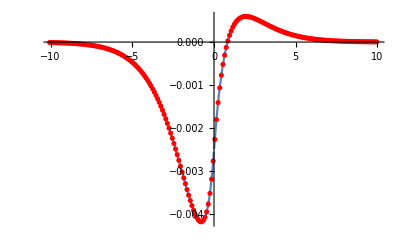
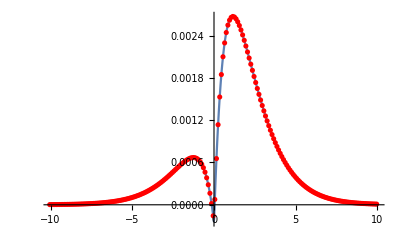

```mathematica
{Show[Plot[χϕcλ[t],{t,-10,10},FrameLabel->"ϕC - λ"],ListPlot[Table[{t,Xϕcλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]],
Show[Plot[χπcλ[t],{t,-10,10},FrameLabel->"πC - λ"],ListPlot[Table[{t,Xπcλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]]}
```

```mathematica
{Show[Plot[χϕyλ[t],{t,-10,10},FrameLabel->"ϕy - λ"],ListPlot[Table[{t,Xϕyλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]],
Show[Plot[χπyλ[t],{t,-10,10},FrameLabel->"πy - λ"],ListPlot[Table[{t,Xπyλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]]}
```

{-Graphics-,-Graphics-}

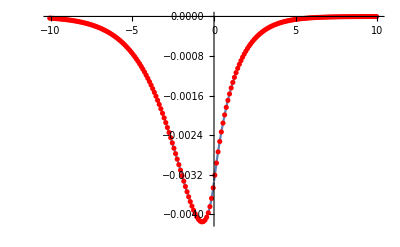
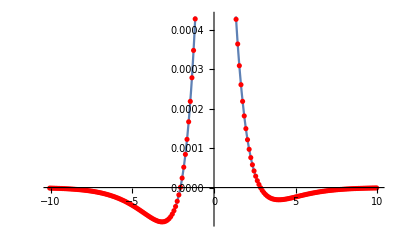

```mathematica
{Show[Plot[χϕhλ[t],{t,-10,10},FrameLabel->"ϕH - λ"],ListPlot[Table[{t,Xϕhλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]],
Show[Plot[χπhλ[t],{t,-10,10},FrameLabel->"πH - λ"],ListPlot[Table[{t,Xπhλ[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]]}
```

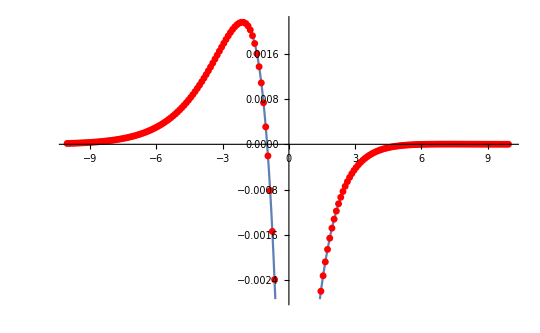

```mathematica
Show[Plot[χπhπy[t],{t,-10,10},FrameLabel->"πH - πY"],ListPlot[Table[{t,Xπhπy[t,{θπc,θs,θπy,θπh,θM,θλ,βπc,βs,βπy,βπh,βM,βλ},{TR,TMπ,TMπh,TCM,TMλ,α1,α2},λ0]},{t,-10.05,10,0.1}],PlotStyle-> Red]]
```

#### Cross-Covariances: Analytical versions vs Decomposed versions

Check Cross-covariances. If the red-dotted lines match the blue curves, both models are equal.

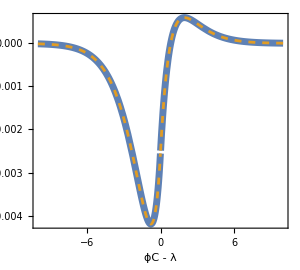
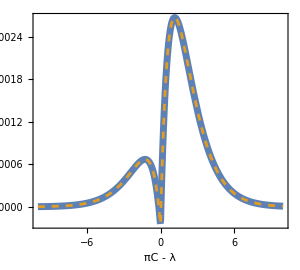

```mathematica
{Plot[{χϕcλ[t],χMϕcλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"ϕC - λ"],
Plot[{χπcλ[t],χMπcλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"πC - λ"]}
```

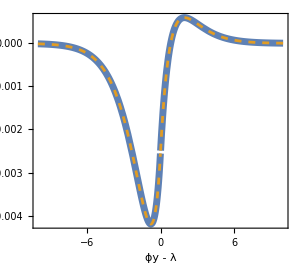
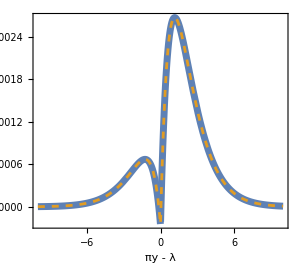

```mathematica
{Plot[{χϕyλ[t],χMϕyλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"ϕy - λ"],
Plot[{χπyλ[t],χMπyλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"πy - λ"]}
```

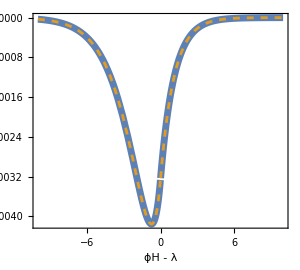
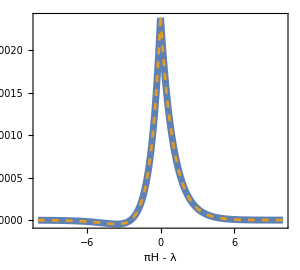

```mathematica
{Plot[{χϕhλ[t],χMϕhλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"ϕH - λ"],
Plot[{χπhλ[t],χMπhλ[t,{1,1,1,1}]},{t,-10,10},FrameLabel->"πH - λ"]}
```